```mathematica
Needs["ErrorBarPlots`"]
```

## PT DATA

```mathematica
qsquaredata={0.49,0.79,1.18,1.48,1.77,1.88,2.47,2.97,3.47,0.32,0.35,0.39,0.46,0.57,0.76,0.86,0.88,1.02,1.12,1.18,1.42,1.76,0.8,1.3,0.5,1,1.6,2.6,3.5,4,4.8,5.6};
muRdata={0.966,0.95,0.869,0.798,0.728,0.72,0.726,0.612,0.609,0.93,0.91,0.961,0.952,0.959,0.966,0.865,0.923,0.9,0.825,0.851,0.733,0.816,0.901,0.858,0.895,0.868,0.992,0.869,0.571,0.517,0.45,0.354}
errormuR = {0.033,0.032,0.041,0.068,0.073,0.091,0.089,0.088,0.092,0.074,0.065,0.038,0.04,0.046,0.045,0.044,0.099,0.06,0.047,0.073,0.087,0.184,0.17,0.27,0.063,0.049,0.05,0.18,0.079,0.064,0.064,0.104};
data=Transpose[{qsquaredata, muRdata}]
errorplot = Transpose[{qsquaredata, muRdata, errormuR}]

errorplusmuR= muRdata+errormuR
errorminusmuR=muRdata-errormuR
errordataplus=Transpose[{qsquaredata, errorplusmuR}]
errordataminus=Transpose[{qsquaredata, errorminusmuR}]
fitplus=Fit[errordataplus,{1,w,w^2,w^3},w]
fitminus=Fit[errordataminus,{1,w,w^2,w^3},w]

muR=1+a*Q2+b*(Q2)^2+c*(Q2)^3
FindFit[data, {muR},{a,b,c},Q2]
```

{0.966,0.95,0.869,0.798,0.728,0.72,0.726,0.612,0.609,0.93,0.91,0.961,0.952,0.959,0.966,0.865,0.923,0.9,0.825,0.851,0.733,0.816,0.901,0.858,0.895,0.868,0.992,0.869,0.571,0.517,0.45,0.354}

{{0.49,0.966},{0.79,0.95},{1.18,0.869},{1.48,0.798},{1.77,0.728},{1.88,0.72},{2.47,0.726},{2.97,0.612},{3.47,0.609},{0.32,0.93},{0.35,0.91},{0.39,0.961},{0.46,0.952},{0.57,0.959},{0.76,0.966},{0.86,0.865},{0.88,0.923},{1.02,0.9},{1.12,0.825},{1.18,0.851},{1.42,0.733},{1.76,0.816},{0.8,0.901},{1.3,0.858},{0.5,0.895},{1,0.868},{1.6,0.992},{2.6,0.869},{3.5,0.571},{4,0.517},{4.8,0.45},{5.6,0.354}}

{{0.49,0.966,0.033},{0.79,0.95,0.032},{1.18,0.869,0.041},{1.48,0.798,0.068},{1.77,0.728,0.073},{1.88,0.72,0.091},{2.47,0.726,0.089},{2.97,0.612,0.088},{3.47,0.609,0.092},{0.32,0.93,0.074},{0.35,0.91,0.065},{0.39,0.961,0.038},{0.46,0.952,0.04},{0.57,0.959,0.046},{0.76,0.966,0.045},{0.86,0.865,0.044},{0.88,0.923,0.099},{1.02,0.9,0.06},{1.12,0.825,0.047},{1.18,0.851,0.073},{1.42,0.733,0.087},{1.76,0.816,0.184},{0.8,0.901,0.17},{1.3,0.858,0.27},{0.5,0.895,0.063},{1,0.868,0.049},{1.6,0.992,0.05},{2.6,0.869,0.18},{3.5,0.571,0.079},{4,0.517,0.064},{4.8,0.45,0.064},{5.6,0.354,0.104}}

{0.999,0.982,0.91,0.866,0.801,0.811,0.815,0.7,0.701,1.004,0.975,0.999,0.992,1.005,1.011,0.909,1.022,0.96,0.872,0.924,0.82,1.,1.071,1.128,0.958,0.917,1.042,1.049,0.65,0.581,0.514,0.458}

{0.933,0.918,0.828,0.73,0.655,0.629,0.637,0.524,0.517,0.856,0.845,0.923,0.912,0.913,0.921,0.821,0.824,0.84,0.778,0.778,0.646,0.632,0.731,0.588,0.832,0.819,0.942,0.689,0.492,0.453,0.386,0.25}

{{0.49,0.999},{0.79,0.982},{1.18,0.91},{1.48,0.866},{1.77,0.801},{1.88,0.811},{2.47,0.815},{2.97,0.7},{3.47,0.701},{0.32,1.004},{0.35,0.975},{0.39,0.999},{0.46,0.992},{0.57,1.005},{0.76,1.011},{0.86,0.909},{0.88,1.022},{1.02,0.96},{1.12,0.872},{1.18,0.924},{1.42,0.82},{1.76,1.},{0.8,1.071},{1.3,1.128},{0.5,0.958},{1,0.917},{1.6,1.042},{2.6,1.049},{3.5,0.65},{4,0.581},{4.8,0.514},{5.6,0.458}}

{{0.49,0.933},{0.79,0.918},{1.18,0.828},{1.48,0.73},{1.77,0.655},{1.88,0.629},{2.47,0.637},{2.97,0.524},{3.47,0.517},{0.32,0.856},{0.35,0.845},{0.39,0.923},{0.46,0.912},{0.57,0.913},{0.76,0.921},{0.86,0.821},{0.88,0.824},{1.02,0.84},{1.12,0.778},{1.18,0.778},{1.42,0.646},{1.76,0.632},{0.8,0.731},{1.3,0.588},{0.5,0.832},{1,0.819},{1.6,0.942},{2.6,0.689},{3.5,0.492},{4,0.453},{4.8,0.386},{5.6,0.25}}

0.984471+0.0298616 w-0.049901 w^2+0.00488625 w^3

0.971653-0.195965 w+0.0284498 w^2-0.00289454 w^3

1+a Q2+b Q2^2+c Q2^3

{a→-0.117237,b→0.00252261,c→-0.000434747}

```mathematica
{a,b,c}/.fitPT
```

{-0.0519834,0.0070918,0.0012399}

1-0.117237 Q2+0.00252261 Q2^2-0.000434747 Q2^3

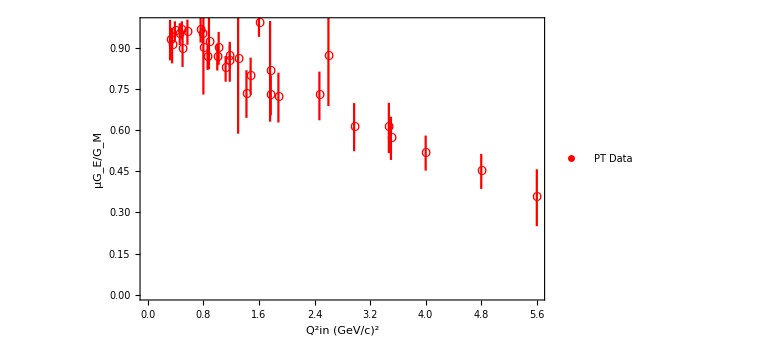

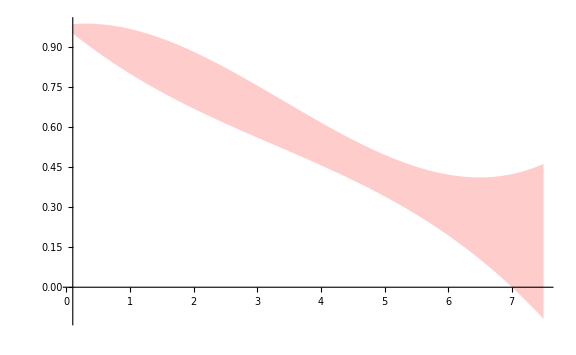

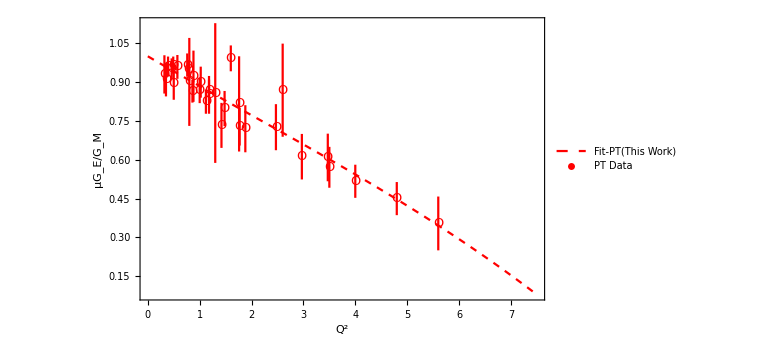

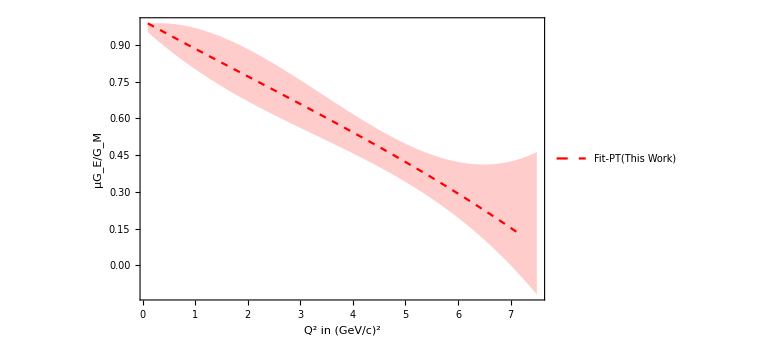

```mathematica
fitPT= 1+(-0.11723721716472688)*Q2+(0.0025226146422440594)*(Q2)^2+(-0.0004347472619650877)*(Q2)^3
plt=ErrorListPlot[Table[{errorplot[[i,{1,2}]],ErrorBar[errorplot[[i,3]]]},{i,1,Length[errorplot]}], PlotStyle->Red,Joined->False,PlotMarkers->{"O", Medium},PlotLegends-> Placed[LineLegend[{"PT Data"},LabelStyle->Directive[Red,Bold,16]],{0.1,0.1}], FrameLabel->{Style["Q^2in (GeV/c)^2",Bold,18],Style["μG_E/G_M",Bold,18]}, Frame-> True,FrameTicks->All, ImageSize-> Large]

plterrorband=Plot[{fitplus,fitminus},{w,0.1,7.5},Filling->{1->{{2},Blend[{Red,White,White,White,White}]}},PlotStyle->None]

Show[Plot[fitPT,{Q2,0,7.5},PlotStyle->{Red,Dashed},PlotLegends-> Placed[LineLegend[{"Fit-PT(This Work)"}],{0.8,0.8}]],plt, PlotRange->All,Frame-> True,FrameTicks->All,FrameLabel->{Style["Q^2",Bold,18],Style["μG_E/G_M",Bold,18]}, Frame-> True,FrameTicks->All, ImageSize-> Large]

Show[plterrorband,Plot[fitPT,{Q2,0.1,7.2},PlotStyle->{Red,Dashed},PlotLegends-> Placed[LineLegend[{"Fit-PT(This Work)"}],{0.8,0.8}]], FrameTicks->All,FrameLabel->{Style["Q^2 in (GeV/c)^2",Bold,18],Style["μG_E/G_M",Bold,18]}, Frame-> True,FrameTicks->All,Axes->False, ImageSize-> Large]
```

## LT DATA

```mathematica
Import["F:\\Fahad Documents\\Dept. of Physics,SUST\\Study Materials\\4-2\\PROJECT PHY428-20220803T021501Z-001\\PROJECT PHY428\\Figures\\Rosenbluth data combined(1994-2005).csv"]
```

{{,Rosenbluth ,,},{,,,},{Q^2,muR,ERROR(mu R),},{1.75,0.911526,0.0737462,Andivahis(1994)},{2.5,0.850474,0.046443,},{3.25,0.844763,0.043889,},{0.65,1.069,0.085,M.E.Cristy (2004)},{0.91,0.928,0.067,},{2.2,0.878,0.125,},{2.75,0.841,0.109,},{3.75,0.837,0.22,},{4.2,1.24,0.163,},{5.2,1.176,0.552,},{0.15,1.012,0.018,RC Walker(1994)},{0.3,1.023,0.018,},{0.45,1.009,0.016,},{0.6,0.984,0.017,},{0.75,0.938,0.025,},{1,0.971,0.026,},{1.25,0.961,0.038,},{1.5,0.993,0.043,},{2,1.03,0.055,},{3,0.951,0.068,},{4,1.058,0.089,},{5,1.006,0.14,},{6,1.028,0.217,},{7,1.468,0.189,},{2.64,0.902,0.038,Qattan(2005)},{3.2,0.961,0.051,},{4.1,1.097,0.077,}}

```mathematica
TableForm[%206]
```

| Rosenbluth  |  | 
 |  |  | 
Q^2 | muR | ERROR(mu R) | 
1.75 | 0.911526 | 0.0737462 | Andivahis(1994)
2.5 | 0.850474 | 0.046443 | 
3.25 | 0.844763 | 0.043889 | 
0.65 | 1.069 | 0.085 | M.E.Cristy (2004)
0.91 | 0.928 | 0.067 | 
2.2 | 0.878 | 0.125 | 
2.75 | 0.841 | 0.109 | 
3.75 | 0.837 | 0.22 | 
4.2 | 1.24 | 0.163 | 
5.2 | 1.176 | 0.552 | 
0.15 | 1.012 | 0.018 | RC Walker(1994)
0.3 | 1.023 | 0.018 | 
0.45 | 1.009 | 0.016 | 
0.6 | 0.984 | 0.017 | 
0.75 | 0.938 | 0.025 | 
1 | 0.971 | 0.026 | 
1.25 | 0.961 | 0.038 | 
1.5 | 0.993 | 0.043 | 
2 | 1.03 | 0.055 | 
3 | 0.951 | 0.068 | 
4 | 1.058 | 0.089 | 
5 | 1.006 | 0.14 | 
6 | 1.028 | 0.217 | 
7 | 1.468 | 0.189 | 
2.64 | 0.902 | 0.038 | Qattan(2005)
3.2 | 0.961 | 0.051 | 
4.1 | 1.097 | 0.077 |

{1.75,2.5,3.25,0.65,0.91,2.2,2.75,3.75,4.2,5.2,0.15,0.3,0.45,0.6,0.75,1,1.25,1.5,2,3,4,5,6,7,2.64,3.2,4.1}

{0.911526,0.850474,0.844763,1.069,0.928,0.878,0.841,0.837,1.24,1.176,1.012,1.023,1.009,0.984,0.938,0.971,0.961,0.993,1.03,0.951,1.058,1.006,1.028,1.468,0.902,0.961,1.097}

{0.0737462,0.046443,0.043889,0.085,0.067,0.125,0.109,0.22,0.163,0.552,0.018,0.018,0.016,0.017,0.025,0.026,0.038,0.043,0.055,0.068,0.089,0.14,0.217,0.189,0.038,0.051,0.077}

{{1.75,0.911526},{2.5,0.850474},{3.25,0.844763},{0.65,1.069},{0.91,0.928},{2.2,0.878},{2.75,0.841},{3.75,0.837},{4.2,1.24},{5.2,1.176},{0.15,1.012},{0.3,1.023},{0.45,1.009},{0.6,0.984},{0.75,0.938},{1,0.971},{1.25,0.961},{1.5,0.993},{2,1.03},{3,0.951},{4,1.058},{5,1.006},{6,1.028},{7,1.468},{2.64,0.902},{3.2,0.961},{4.1,1.097}}

{{1.75,0.911526,0.0737462},{2.5,0.850474,0.046443},{3.25,0.844763,0.043889},{0.65,1.069,0.085},{0.91,0.928,0.067},{2.2,0.878,0.125},{2.75,0.841,0.109},{3.75,0.837,0.22},{4.2,1.24,0.163},{5.2,1.176,0.552},{0.15,1.012,0.018},{0.3,1.023,0.018},{0.45,1.009,0.016},{0.6,0.984,0.017},{0.75,0.938,0.025},{1,0.971,0.026},{1.25,0.961,0.038},{1.5,0.993,0.043},{2,1.03,0.055},{3,0.951,0.068},{4,1.058,0.089},{5,1.006,0.14},{6,1.028,0.217},{7,1.468,0.189},{2.64,0.902,0.038},{3.2,0.961,0.051},{4.1,1.097,0.077}}

{0.985272,0.896917,0.888652,1.154,0.995,1.003,0.95,1.057,1.403,1.728,1.03,1.041,1.025,1.001,0.963,0.997,0.999,1.036,1.085,1.019,1.147,1.146,1.245,1.657,0.94,1.012,1.174}

{0.83778,0.804031,0.800874,0.984,0.861,0.753,0.732,0.617,1.077,0.624,0.994,1.005,0.993,0.967,0.913,0.945,0.923,0.95,0.975,0.883,0.969,0.866,0.811,1.279,0.864,0.91,1.02}

{{1.75,0.985272},{2.5,0.896917},{3.25,0.888652},{0.65,1.154},{0.91,0.995},{2.2,1.003},{2.75,0.95},{3.75,1.057},{4.2,1.403},{5.2,1.728},{0.15,1.03},{0.3,1.041},{0.45,1.025},{0.6,1.001},{0.75,0.963},{1,0.997},{1.25,0.999},{1.5,1.036},{2,1.085},{3,1.019},{4,1.147},{5,1.146},{6,1.245},{7,1.657},{2.64,0.94},{3.2,1.012},{4.1,1.174}}

{{1.75,0.83778},{2.5,0.804031},{3.25,0.800874},{0.65,0.984},{0.91,0.861},{2.2,0.753},{2.75,0.732},{3.75,0.617},{4.2,1.077},{5.2,0.624},{0.15,0.994},{0.3,1.005},{0.45,0.993},{0.6,0.967},{0.75,0.913},{1,0.945},{1.25,0.923},{1.5,0.95},{2,0.975},{3,0.883},{4,0.969},{5,0.866},{6,0.811},{7,1.279},{2.64,0.864},{3.2,0.91},{4.1,1.02}}

1.11987-0.198377 w+0.0693703 w^2-0.00440596 w^3

0.981367-0.0281185 w-0.017655 w^2+0.00365293 w^3

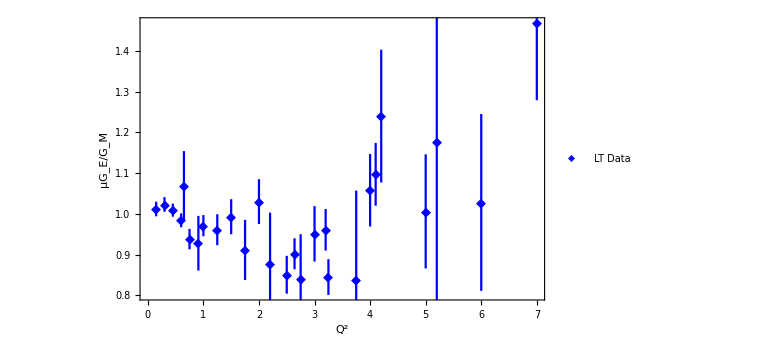

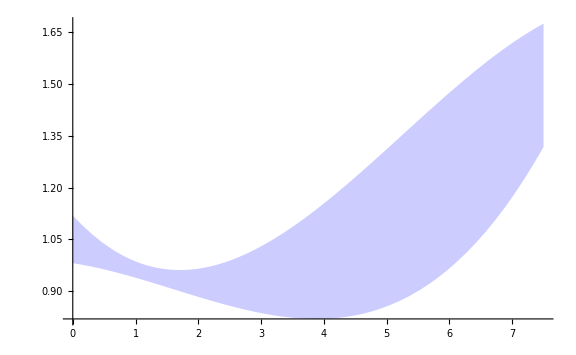

1+a Q2+b Q2^2+c Q2^3

{a→-0.0519834,b→0.0070918,c→0.0012399}

```mathematica
ltq2data={1.75,2.5,3.25,0.65,0.91,2.2,2.75,3.75,4.2,5.2,0.15,0.3,0.45,0.6,0.75,1,1.25,1.5,2,3,4,5,6,7,2.64,3.2,4.1}
ltmuRdata={0.911526,0.850474,0.844763,1.069,0.928,0.878,0.841,0.837,1.24,1.176,1.012,1.023,1.009,0.984,0.938,0.971,0.961,0.993,1.03,0.951,1.058,1.006,1.028,1.468,0.902,0.961,1.097}
lterrormuR={0.0737462,0.046443,0.043889,0.085,0.067,0.125,0.109,0.22,0.163,0.552,0.018,0.018,0.016,0.017,0.025,0.026,0.038,0.043,0.055,0.068,0.089,0.14,0.217,0.189,0.038,0.051,0.077}
ltdata = Transpose[{ltq2data, ltmuRdata}]
lterrorplot= Transpose[{ltq2data, ltmuRdata, lterrormuR}]
LTerrorplusmuR= ltmuRdata+lterrormuR
LTerrorminusmuR=ltmuRdata-lterrormuR
LTerrordataplus=Transpose[{ltq2data, LTerrorplusmuR}]
LTerrordataminus=Transpose[{ltq2data, LTerrorminusmuR}]
LTfitplus=Fit[LTerrordataplus,{1,w,w^2,w^3},w]
LTfitminus=Fit[LTerrordataminus,{1,w,w^2,w^3},w]
ltplot=ErrorListPlot[Table[{lterrorplot[[i,{1,2}]],ErrorBar[lterrorplot[[i,3]]]},{i,1,Length[lterrorplot]}], PlotStyle->Blue,Joined->False,PlotMarkers->{"◆", Medium}, FrameLabel->{Style["Q^2",Bold,18],Style["μG_E/G_M",Bold,18]},PlotLegends-> Placed[LineLegend[{"LT Data"},LabelStyle->Directive[Blue,Bold,16]],{0.1,0.9}], Frame-> True,FrameTicks->All, ImageSize-> Large,FrameTicksStyle-> Directive[Black,14]]

LTplterrorband=Plot[{LTfitplus,LTfitminus},{w,0,7.5},Filling->{1->{{2},Blend[{Blue,White,White,White,White}]}},PlotStyle->None,FrameTicksStyle-> Directive[Black,14]]

muR=1+a*Q2+b*(Q2)^2+c*(Q2)^3
fitPT=FindFit[ltdata, {muR},{a,b,c},Q2]
```

```mathematica
1+a Q2+b Q2^2+c Q2^3/.fitPT
```

1-0.0519834 Q2+0.0070918 Q2^2+0.0012399 Q2^3

1-0.0519834 Q2+0.0070918 Q2^2+0.0012399 Q2^3

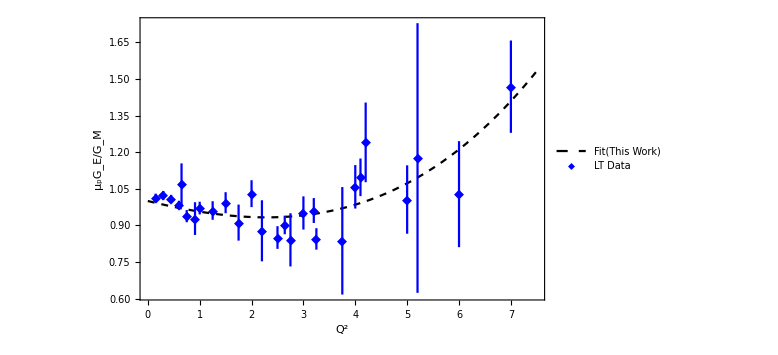

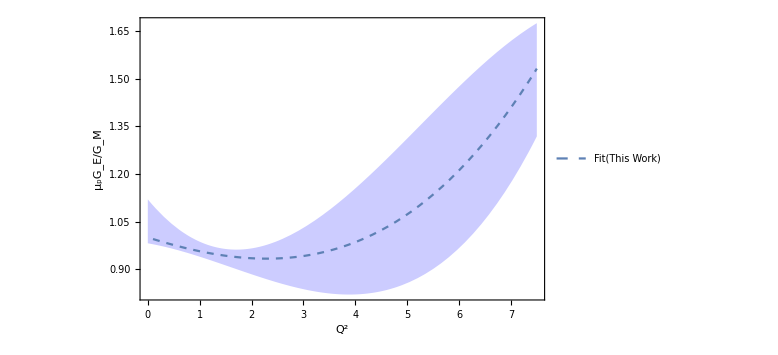

```mathematica
ltfitA=1+(-0.05198337828047632)*Q2+(0.007091802442190973)*(Q2)^2+(0.0012399017660881329)*(Q2)^3
Show[Plot[ltfitA,{Q2,0,7.5},PlotStyle->{Black,Dashed},PlotLegends-> Placed[LineLegend[{"Fit(This Work)"}],{0.8,0.95}]],ltplot, PlotRange->All,Frame-> True,FrameTicks->All,FrameLabel->{Style["Q^2",Bold,18],Style["μ_pG_E/G_M",Bold,18]}, Frame-> True,FrameTicks->All, Axes->False,ImageSize-> Large]

Show[LTplterrorband,Plot[ltfitA,{Q2,0.1,7.5},PlotStyle->Dashed,PlotLegends-> Placed[LineLegend[{"Fit(This Work)"}],{0.8,0.9}]], PlotRange->All,Frame-> True,FrameTicks->All,FrameLabel->{Style["Q^2",Bold,18],Style["μ_pG_E/G_M",Bold,18]}, Frame-> True,FrameTicks->All,Axes->False, ImageSize-> Large]
```

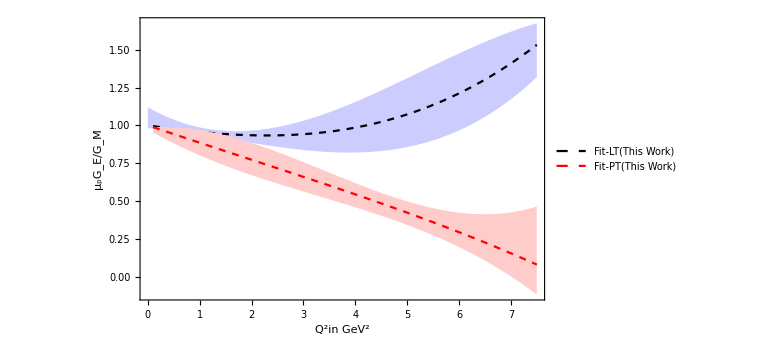

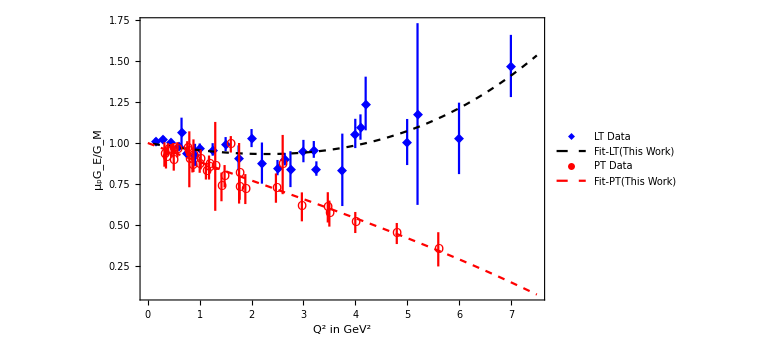

```mathematica
Show[ LTplterrorband,Plot[ltfitA,{Q2,0.1,7.5},PlotStyle->{Black,Dashed},PlotLegends-> Placed[LineLegend[{"Fit-LT(This Work)"},LabelStyle->Directive[Black,Bold,14]],{0.2,0.9}]], plterrorband,Plot[fitPT,{Q2,0.1,7.5},PlotStyle->{Red,Dashed},PlotLegends-> Placed[LineLegend[{"Fit-PT(This Work)"},LabelStyle->Directive[Red,Bold,14]],{0.2,0.8}]],PlotRange->All,Frame-> True,FrameTicks->All,FrameLabel->{Style["Q^2in GeV^2",Bold,18,Black],Style["μ_pG_E/G_M",Bold,18,Black]}, Frame-> True,FrameTicks->All,Axes->False, ImageSize-> Large,FrameTicksStyle-> Directive[Black,14]]                        

Show[ltplot,Plot[ltfitA,{Q2,0.1,7.5},PlotStyle->{Black,Dashed},PlotLegends-> Placed[LineLegend[{"Fit-LT(This Work)"},LabelStyle->Directive[Black,Bold,14]],{0.4,0.9}]], plt,Plot[fitPT,{Q2,0,7.5},PlotStyle->{Red,Dashed},PlotLegends-> Placed[LineLegend[{"Fit-PT(This Work)"},LabelStyle->Directive[Red,Bold,14]],{0.4,0.8}]],PlotRange->All,Frame-> True,FrameTicks->All,FrameLabel->{Style["Q^2 in GeV^2",Bold,18,Black],Style["μ_pG_E/G_M",Bold,18,Black]}, Frame-> True,FrameTicks->All,Axes->False, ImageSize-> Large,FrameTicksStyle-> Directive[Black,14]]
```